```mathematica
(*Import the video and set videoFrames to the image list of frames *)

filename="E:\\Cavendish\\runs\\run2.MOV";
frames=Import[filename,"ImageList"];
```

```mathematica
(*Get video dimensions for cropping*)
Manipulate[ImageTake[frames[[1]],{a,b},{c,d}],{a,1,1080},{b,2,1080},{c,1,1920},{d,2,1920}]
```

```mathematica
(*Cropping the image *)
length=Length[frames];
ymin=230;
ymax=324;
xmin=1;
xmax=1920;
croppedFrames=Table[ImageTake[frames[[i]],{ymin,ymax},{xmin,xmax}],{i,length}];
```

```mathematica
(*Show crop*)
```

```mathematica
croppedFrames[[1]]
```

-Graphics-

```mathematica
length
```

681

```mathematica
(*Use binarize to create a binary image set*)
```

```mathematica
binarizedFrames=Table[Binarize[croppedFrames[[i]],.5],{i,length}];
newBinarizedFrames=Table[DeleteSmallComponents[binarizedFrames[[i]]],{i,length}];
```

```mathematica
(*Get coordinates for the pixels*)
```

```mathematica
help=Table[ComponentMeasurements[newBinarizedFrames[[i]],"Centroid"],{i,length}]//Values;
xvals=Flatten[help[[;;,;;,1]]];
yvals=Flatten[help[[;;,;;,2]]];
```

```mathematica
(*Plot*)
```

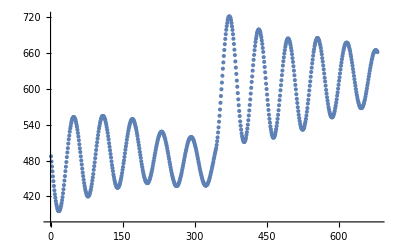

```mathematica
ListPlot[Transpose[xvals]]
```

```mathematica
run2data=Transpose@{xvals}

Export["E:\\Cavendish\\runs\\run2data.csv",run2data,"CSV"]
```

{{487.056},{478.333},{470.},{462.},{453.5},{445.5},{437.5},{430.214},{423.75},{418.},{412.3},{407.5},{403.786},{400.},{397.5},{395.833},{395.5},{395.5},{396.75},{398.667},{401.3},{404.7},{408.5},{413.5},{418.875},{425.333},{432.},{439.},{446.5},{454.},{462.167},{469.7},{477.5},{485.75},{493.5},{500.75},{508.389},{515.5},{521.75},{528.214},{533.643},{537.786},{542.5},{546.},{549.3},{550.7},{552.3},{552.7},{552.5},{551.7},{549.7},{548.},{544.5},{540.667},{536.5},{531.5},{526.071},{520.333},{514.},{507.2},{500.5},{494.214},{487.},{480.125},{473.357},{466.5},{459.929},{454.},{448.},{442.375},{437.5},{433.},{429.214},{426.3},{423.5},{421.833},{420.3},{420.},{420.3},{421.7},{422.833},{425.3},{428.5},{431.75},{436.25},{440.875},{446.333},{451.667},{457.5},{464.5},{470.7},{477.},{484.},{490.7},{497.667},{504.5},{510.625},{516.833},{522.625},{528.375},{533.667},{537.786},{542.375},{546.1},{549.3},{551.3},{553.5},{554.5},{554.375},{554.389},{553.625},{552.},{549.7},{548.},{544.214},{540.375},{535.9},{531.333},{526.333},{520.786},{515.375},{508.875},{503.},{497.071},{491.},{485.1},{478.5},{472.5},{467.5},{462.333},{456.5},{452.5},{448.},{444.333},{441.25},{439.1},{437.},{435.333},{434.7},{434.5},{435.214},{436.3},{438.},{439.833},{443.},{446.5},{450.333},{454.333},{459.1},{464.333},{469.214},{475.25},{480.25},{486.125},{492.214},{498.167},{503.786},{509.056},{514.944},{520.1},{524.643},{529.5},{533.667},{537.167},{540.625},{543.214},{545.5},{547.7},{548.667},{549.167},{549.333},{548.667},{547.7},{545.5},{543.5},{540.643},{537.},{534.333},{530.214},{525.5},{521.071},{515.625},{510.833},{505.7},{500.357},{494.5},{489.357},{484.5},{478.667},{473.786},{469.214},{464.5},{460.375},{456.5},{453.},{450.5},{447.625},{445.5},{444.333},{443.},{442.375},{442.375},{442.357},{443.75},{445.333},{447.375},{449.667},{452.5},{455.5},{459.},{462.5},{466.5},{470.786},{475.5},{479.5},{484.3},{488.7},{492.944},{497.5},{501.7},{505.7},{509.625},{513.333},{516.214},{519.333},{521.5},{523.875},{525.5},{526.833},{527.75},{528.214},{528.214},{527.625},{526.333},{525.071},{522.944},{520.7},{517.833},{515.375},{511.643},{508.071},{504.625},{500.214},{495.643},{491.5},{486.722},{482.5},{477.5},{473.357},{468.833},{464.5},{460.375},{456.5},{453.},{450.3},{447.214},{444.5},{442.167},{440.},{439.},{437.7},{437.5},{437.5},{437.7},{438.7},{439.722},{441.833},{443.786},{446.5},{449.5},{452.5},{455.7},{459.3},{463.5},{467.5},{471.5},{475.786},{479.944},{484.3},{488.5},{492.5},{496.333},{499.667},{503.333},{506.786},{509.625},{512.25},{514.3},{516.214},{517.5},{518.375},{519.333},{519.333},{519.},{518.167},{517.5},{515.5},{514.},{511.357},{508.643},{505.5},{502.5},{499.214},{495.214},{491.333},{487.25},{483.167},{478.7},{475.071},{470.7},{466.5},{462.357},{459.167},{455.7},{452.5},{449.5},{446.5},{444.5},{442.167},{440.5},{439.375},{438.667},{438.},{438.214},{438.667},{439.5},{440.5},{442.375},{444.5},{446.5},{449.7},{452.167},{455.7},{459.3},{462.357},{466.5},{470.3},{474.},{477.75},{482.357},{485.929},{490.071},{493.5},{497.333},{500.8},{506.071},{512.333},{518.667},{527.},{535.5},{545.},{554.9},{565.357},{576.625},{587.944},{599.25},{610.375},{621.833},{633.667},{644.136},{654.944},{664.955},{674.6},{683.389},{691.375},{698.7},{704.75},{709.875},{714.75},{718.},{720.25},{721.},{721.},{720.056},{718.333},{714.5},{709.833},{704.375},{698.5},{691.375},{683.75},{675.},{665.389},{656.389},{645.773},{635.5},{624.944},{613.722},{603.5},{592.833},{582.357},{572.5},{562.875},{554.389},{545.5},{538.25},{531.75},{525.5},{520.667},{516.833},{514.},{511.833},{511.125},{511.056},{512.625},{514.625},{517.833},{522.7},{527.5},{533.5},{540.},{547.5},{555.3},{563.75},{573.},{582.214},{592.},{601.667},{611.5},{620.667},{630.375},{639.5},{648.5},{656.722},{664.591},{671.625},{678.3},{683.786},{688.3},{692.833},{695.625},{697.625},{698.944},{699.278},{698.375},{696.611},{694.389},{690.5},{686.25},{680.917},{675.071},{668.357},{661.625},{653.},{645.},{636.5},{627.643},{618.},{608.5},{599.625},{590.409},{581.5},{573.},{564.7},{556.667},{549.7},{543.357},{537.167},{532.214},{527.5},{523.833},{521.3},{519.3},{518.056},{518.5},{519.5},{521.5},{524.25},{528.357},{532.625},{537.667},{543.357},{549.7},{556.5},{564.214},{572.5},{581.},{588.611},{597.6},{606.},{614.214},{622.833},{630.5},{638.833},{646.045},{652.625},{659.056},{664.591},{670.071},{674.167},{678.},{680.591},{682.625},{683.786},{684.214},{683.5},{682.},{679.833},{676.5},{673.278},{668.389},{663.682},{657.955},{651.375},{644.962},{637.75},{630.357},{622.625},{614.5},{606.5},{599.056},{591.},{583.167},{576.333},{569.214},{562.7},{556.5},{551.},{546.1},{541.5},{537.786},{534.786},{533.333},{532.375},{531.5},{531.833},{532.929},{534.5},{537.5},{541.5},{545.125},{549.7},{555.3},{561.5},{567.786},{575.3},{581.643},{589.375},{597.269},{605.},{612.375},{620.25},{628.056},{635.25},{642.5},{648.7},{655.375},{661.625},{666.136},{671.333},{675.167},{678.625},{681.1},{682.722},{684.667},{684.929},{684.667},{683.278},{681.4},{679.375},{675.611},{672.5},{668.214},{663.},{657.75},{651.357},{645.4},{639.},{632.5},{625.643},{618.5},{612.333},{605.3},{598.214},{591.955},{585.833},{580.1},{574.7},{569.357},{565.5},{561.5},{558.25},{556.},{553.833},{552.7},{552.333},{552.333},{553.357},{554.611},{557.167},{560.},{563.167},{567.75},{571.786},{577.},{582.333},{588.5},{594.},{600.214},{606.625},{613.357},{619.25},{625.75},{632.214},{638.4},{643.864},{649.5},{654.6},{659.056},{663.714},{667.},{670.5},{673.},{675.071},{676.5},{677.},{677.2},{676.917},{676.25},{674.5},{672.5},{669.625},{666.3},{662.955},{658.167},{654.1},{649.},{643.864},{638.611},{633.},{627.667},{621.625},{616.},{610.375},{605.167},{599.643},{594.5},{589.833},{585.5},{581.5},{578.},{575.5},{572.389},{570.214},{568.833},{567.9},{567.7},{567.833},{568.357},{569.5},{571.667},{573.5},{576.5},{579.7},{582.786},{587.},{591.4},{595.786},{600.5},{605.75},{610.214},{615.5},{620.5},{625.375},{630.375},{634.962},{639.5},{643.389},{647.786},{651.},{654.7},{657.75},{660.},{661.667},{663.},{664.278},{664.5},{664.5},{664.1},{662.8},{661.5}}

E:\Cavendish\runs\run2data.csv